```mathematica
computeLeakageProfile[z_List,left_,right_,pe_]:=Module[{res,i,n=Length[right]-1},res=ConstantArray[0,Length[z]];
Do[mask=MapThread[Boole[#1>=right[[i]]&&#1<left[[i+1]]]&,{z}];
res+=mask*(pe[[i]]-pe[[i+1]]);,{i,1,n}];
res]

calculateDeviationMetric[z_List,foundLeft_,foundRight_,trueLeft_,trueRight_,peTrue_,peOpt_]:=Module[{stepOpt,stepTrue,squaredDiff,normFactor,area,L},stepOpt=computeLeakageProfile[z,foundLeft,foundRight,peOpt];
stepTrue=computeLeakageProfile[z,trueLeft,trueRight,peTrue];
normFactor=Max[Abs[stepTrue]];
normFactor=If[normFactor==0,1.0,normFactor];
squaredDiff=((stepOpt-stepTrue)/normFactor)^2;
area=NIntegrate[Interpolation[Transpose[{z,squaredDiff}]][x],{x,Min[z],Max[z]}];
L=Max[z]-Min[z];
Sqrt[area/L]]
```

```mathematica
ПАРАМЕТРЫ
```

```mathematica
z=Subdivide[0,550,500];
trueLeft={100,250, 400};
trueRight={200,350,550};
peTrue={5000,1000,0};

foundLeft={100,248, 401};
foundRight={202,354,550};
peOpt={5000,900,0};

calculateDeviationMetric[z,foundLeft,foundRight,trueLeft,trueRight,peTrue,peOpt] // FullSimplify
```

(√1373)/400

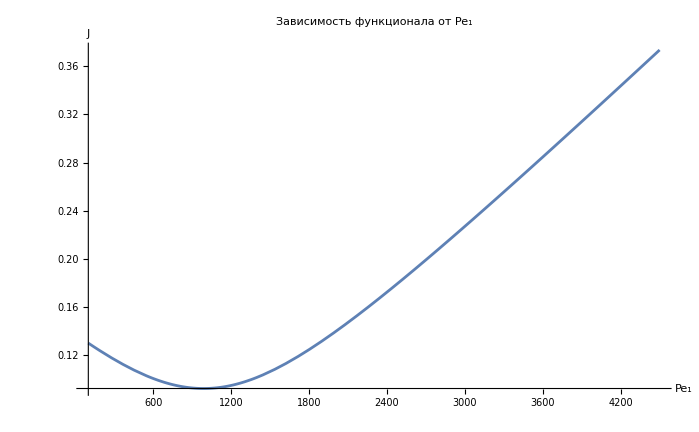

```mathematica
Plot[calculateDeviationMetric[z,foundLeft,foundRight,trueLeft,trueRight,peTrue,{5000,pe,0}],{pe,100,4500},AxesLabel->{Style["Pe₁",FontFamily->"Times New Roman",FontSize->20],Style["J",FontFamily->"Times New Roman",FontSize->20]},PlotLabel->Style["Зависимость функционала от Pe₁", FontFamily->"Times New Roman",FontSize->20]]
```

```mathematica
p1min=5000;
p2min=1000;
jmin=calculateDeviationMetric[z,foundLeft,foundRight,trueLeft,trueRight,peTrue,{p1min,p2min,0}];

Show[Plot3D[calculateDeviationMetric[z,foundLeft,foundRight,trueLeft,trueRight,peTrue,{p1,p2,0}],{p1,1000,10000},{p2,100,2500},AxesLabel->{Style["Pe₁",FontFamily->"Times New Roman",FontSize->18],Style["Pe₂",FontFamily->"Times New Roman",FontSize->18],Style["J",FontFamily->"Times New Roman",FontSize->18]},PlotLabel->Style["Функционал невязки J(Pe₁, Pe₂)",FontFamily->"Times New Roman",FontSize->20],BaseStyle->{FontFamily->"Times New Roman",FontSize->14},TicksStyle->Directive[FontFamily->"Times New Roman",FontSize->12]],Graphics3D[{Red,PointSize[Large],Point[{p1min,p2min,jmin}]}]]
```

-Graphics3D-